## Example: Least Action

Consider throwing a ball vertically upwards in a gravitational field (a==-g) at t=0 and catching it at t=3. Choose the zero of potential at y=0 and measure its height as a function of time y(t) upwards from this point, that is y(0)==y(3)==0. Ignore air friction.

The Lagrangian L==T-V is the difference between the kinetic energy T and the potential energy V. The Lagrangian for the ball reads

```mathematica
L[y_,t_]:=1/2 m y'[t]^2-m g y[t]
```

The least value of the action, S= ∫_0^3 L(t)ⅆt, determines the trajectory y(t).

Explain why y_α(t)=α t (3-t) is a suitable guess for the trajectory. [3 Marks]

Compute the action S(α) and find the least value of the action by solving S'(α)==0 (do not insert a numerical value for g). Comment on your answer. [2 Marks]

#### Solution

Since

T=1/2 m (y'(t))^2

and

V=m g y(t)

the Lagrangian is

L=1/2 m (y'(t))^2-m g y(t)

The Euler-Lagrange equation, (∂L)/(∂y)-ⅆ/ⅆt(∂L)/(∂y')==0, yields

(∂L)/(∂y)==-m g,(∂L)/(∂y')==m y'⟹ⅆ/ⅆt(∂L)/(∂y')==m y''⟹ m g+m y''==0

Using Mathematica,

```mathematica
(∂L(y,t))/(∂y(t))-D[(∂L(y,t))/(∂y'(t)), t]==0//Simplify
```

m (g+y''(t))==0

The function

```mathematica
Subscript[y, α_][t_]=α t (3-t);
```

is a suitable guess for the trajectory because it

satisfies the boundary conditions

```mathematica
Subscript[y, α][0]==Subscript[y, α][3]==0
```

True

looks qualitatively like the expected solution.

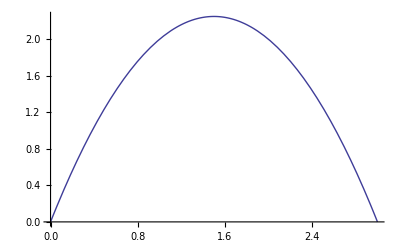

```mathematica
Plot[Subscript[y, 1][t],{t,0,3}]
```

leads to simple evaluation of the functional S.

Define the action S[y]:

```mathematica
S[y_]:=∫_0^3 (1/2 m y'[t]^2-m g y[t])ⅆt
```

Compute the derivative with respect to α of the action, ∂_α S[y_α]:

```mathematica
D[S[Subscript[y, α]], α]//Factor
```

-9/2 m (g-2 α)

we see that ∂_α S[y_α]==0 ⟹ α=g/2,

```mathematica
αval=First@Solve[%==0,α]
```

{α→g/2}

and y(t)=1/2 g  t (3-t),

```mathematica
y[t_]=Subscript[y, α][t]/.αval
```

1/2 g (3-t) t

This is the exact answer to this problem.

```mathematica
y''[t]==-g
```

True

The least value of the action is

```mathematica
S[Subscript[y, α]]/.αval
```

-(9 g^2 m)/8

The following Manipulate example displays the trajectory, the action S, the acceleration, and the energy for m=0.2 kg for the trajectory obtained by linear, quadratic, or cubic interpolation of the Locator points, along with the boundary conditions.

```mathematica
Manipulate[DynamicModule[{pts=Table[{x,0},{x,2}],h,m=0.2,g=9.8,s},

Grid[{{
LocatorPane[Dynamic[pts],Dynamic[h=Evaluate[Interpolation[Sort@Join[{{0,0},{3,0}},pts],InterpolationOrder->n]];s=NIntegrate[1/2 m h'[t]^2-m g h[t], {t, 0, 3},PrecisionGoal->3,AccuracyGoal->3];Plot[{Tooltip[h[t],𝒽[t]],Tooltip[(1/2 m h'[t]^2+m g h[t]), "Energy"],Tooltip[h''[t],"Acceleration"]},{t,0,3},AxesLabel->{t,""},PlotRange->{-15.1,25.1},GridLines->{Dynamic[Join[{0,3},First/@pts]],Range[-15,25,5]},ImageSize->350,AspectRatio->1/2,Epilog->{AbsolutePointSize[10],Point/@{{0,0},{3,0}}},Background->LightGray]],LocatorAutoCreate->All],

Graphics[{GrayLevel[0.5],Tooltip[Polygon[{{0,0},{1,0},{1,s},{0,s},{0,0}}],s],
{Green,Line[{{0,s},{1,s}}],Black,Text[Dynamic@s,{1/2,s-0.5}]}
},AspectRatio->3,ImageSize->50,PlotRange->{-24,0},PlotLabel->"Action"]

}}]],

{{n,1,"Interpolation order"},Range[3]}]
```

Using linear (first order) interpolation (i.e., a straight line fit between adjacent points), move the locators (initially located at t=1 and t=2) so as to reduce the action. Place your mouse over each curves to see which one is which.

What is the acceleration? What can you say about the energy? [2 Marks]

Next try quadratic interpolation and determine the trajectory as accurately as you can by minimizing the action.

What is the value of the least action? Compare the value you obtain to that computed in the first exercise. [2 Marks]

Finally try cubic interpolation and determine the trajectory as accurately as you can.

Describe what happens to the acceleration as you move the Locator points. What is the value of the least action? [2 Marks]

### For the physical trajectory, both the energy and the acceleration are constant.

### You can refine the trajectory by adding additional Locator points: any mouse click that does not hit an existing Locator creates a new locator (look up LocatorAutoCreate).

#### Solution

For linear interpolation — a straight line fit between adjacent points — the acceleration is zero. The energy is piecewise linear.

Using quadratic interpolation the acceleration is piecewise linear, approximately -10, and the energy is almost constant.

The least value of the action is S≈-21.6, which agrees well with the value obtained above.

Using cubic interpolation, the acceleration is linear. It is straightforward to obtain an accurate trajectory.